Autor: Karolina Tatarczyk

# Metody numeryczne w technice

## (kierunek Matematyka)

## Projekt 7

Metoda różnic skończonych

Napisać procedurę realizującą metodę różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego. Działanie procedury przetestować na przykładzie podanym na wykładzie.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia brzegowego:

{m y''(x)+ k y'(x) +s y(x)=0,  x∈[0,10],
y(0)=1, y(10)=1,

Obliczenia wykonać dla dwóch zestawów danych:
a) m=1, k=3, s=2;
b) m=5, k=2, s=10.

Za każdym razem obliczenia wykonać dla 500 i 1000 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek oraz zestawić je na wykresie słupkowym, np. postaci:

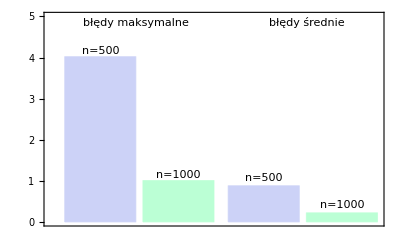

## Rozwiązanie

```mathematica
ClearAll["Global`*"]
FDM[alpha1_,alpha2_,beta1_, beta2_,A_,B_,Ta_,Tb_,M_,K_,S_,Dv_, number_]:=Module[{m=M,k=K,s=S,a1=alpha1,a2=alpha2,b1=beta1,b2=beta2, a=A, b=B, ta=Ta, tb=Tb,n=number,d=Dv,bresult},
h=(b-a)/n;
X=Table[a+i*h,{i,0,n}];
vectorA=Table[m[X[[i]]],{i,1,n}];
vectorB=Table[k[X[[i]]],{i,1,n}];
vectorC=Table[s[X[[i]]],{i,1,n}];
vectorD=Table[d[X[[i]]],{i,1,n}];
(*Uy=bresult*)
bresult={2*h*ta};
For[i=2,i≤n,i++,AppendTo[bresult,2*h*h*vectorD[[i]]]];
AppendTo[bresult, 2*h*tb];
Umatrix=Table[Table[0,{i,1,n+1}],{i,1,n+1}];
Umatrix[[1,1]]=2*h*a1-3*a2;
Umatrix[[1,2]]=4*a2;
Umatrix[[1,3]]=-a2;
Umatrix[[n+1,n-1]]=b2;
Umatrix[[n+1,n]]=-4*b2;
Umatrix[[n+1,n+1]]=2*h*b1+3*b2;
For[i=2,i≤n,i++,
Umatrix[[i,i-1]]=2*vectorA[[i]]-h*vectorB[[i]];
Umatrix[[i,i]]=2*h*h*vectorC[[i]]-4*vectorA[[i]];
Umatrix[[i,i+1]]=2*vectorA[[i]]+h*vectorB[[i]];
];
result=LinearSolve[Umatrix, bresult];

Return[Transpose[{X,result}]]
]
```

### Example - wykład

```mathematica
alpha1=1;
alpha2=1;
beta1=1;
beta2=1;
A=0;
B=4;
Ta=1;
Tb=25;
M[x_]=x*x;
K[x_]=-3*x;
S[x_]=5;
Dv[x_]=x*x+5;
number=4;
r=FDM[alpha1,alpha2,beta1, beta2,A,B,Ta,Tb,M,K,S,Dv, number]
```

{{0,1},{1,2},{2,5},{3,10},{4,17}}

### Example a)

#### n=500

```mathematica
alpha1=1;
alpha2=0;
beta1=1;
beta2=0;
A=0;
B=10;
Ta=1;
Tb=1;
M[x_]=1;
K[x_]=3;
S[x_]=2;
Dv[x_]=0;
a500=FDM[alpha1,alpha2,beta1, beta2,A,B,Ta,Tb,M,K,S,Dv, 500];
p500=ListPlot[a500];
fa[x_]=DSolve[{y''[x]+3*y'[x]+2y[x]==0, y[0]==1,y[10]==1},y[x],x][[1,1,2]];
asolution=Plot[fa[x],{x,0,10},PlotStyle->Orange];
Show[asolution,p500]
```

-Graphics-

```mathematica
ListX500=Transpose[a500][[1]];
aListY500=Transpose[a500][[2]];
aresultPoints500 =  Table[fa[x] /. {x -> ListX500[[i]]}, {i, 1, Length[ListX500]}] ;
abladbezwzgledny500 =  Abs[aListY500 - aresultPoints500] ;
abar500=ListPlot[Transpose[{ListX500,abladbezwzgledny500}], PlotStyle->Orange, Filling->Axis];
```

#### n=1000

```mathematica
a1000=FDM[alpha1,alpha2,beta1, beta2,A,B,Ta,Tb,M,K,S,Dv, 1000];
Show[asolution,ListPlot[a1000]]
```

-Graphics-

### Błędy rozwiązań

```mathematica
ListX1000=Transpose[a1000][[1]];
aListY1000=Transpose[a1000][[2]];
aresultPoints1000 =  Table[fa[x] /. {x -> ListX1000[[i]]}, {i, 1, Length[ListX1000]}] ;
abladbezwzgledny1000 =  Abs[aListY1000 - aresultPoints1000] ;
abar1000=ListPlot[Transpose[{ListX1000,abladbezwzgledny1000}], PlotStyle->Blue, Filling->Axis];
```

```mathematica
Show[abar500,abar1000]
```

-Graphics-

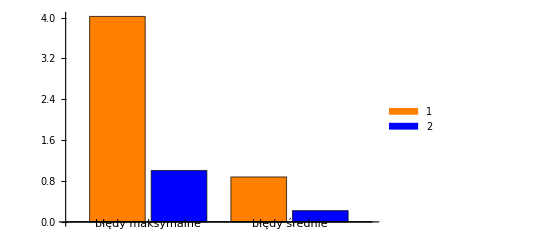

```mathematica
BarChart[{{N[Max[abladbezwzgledny500]], N[Max[abladbezwzgledny1000]]}, {N[Mean[abladbezwzgledny500]], N[Mean[abladbezwzgledny1000]]}}, ChartLabels -> {{"błędy maksymalne", "błędy średnie"},None},ChartStyle->{Orange,Blue}, ChartLegends->{"n=500", "n=1000"}]
```

### Example b)

#### n=500

```mathematica
M[x_]=5;
K[x_]=2;
S[x_]=10;
fb[x_]=DSolve[{5*y''[x]+2*y'[x]+10*y[x]==0, y[0]==1,y[10]==1},y[x],x][[1,1,2]];
bsolution=Plot[fb[x],{x,0,10},PlotStyle->Orange];
b500=FDM[alpha1,alpha2,beta1, beta2,A,B,Ta,Tb,M,K,S,Dv, 500];
Show[bsolution,ListPlot[b500]]
```

-Graphics-

```mathematica
bListY500=Transpose[b500][[2]];
bresultPoints500 =  Table[fb[x] /. {x -> ListX500[[i]]}, {i, 1, Length[ListX500]}] ;
bbladbezwzgledny500 =  Abs[bListY500 - bresultPoints500] ;
bbar500=ListPlot[Transpose[{ListX500,bbladbezwzgledny500}], PlotStyle->Orange, Filling->Axis];
```

#### n=1000

```mathematica
b1000=FDM[alpha1,alpha2,beta1, beta2,A,B,Ta,Tb,M,K,S,Dv, 1000];
Show[bsolution,ListPlot[b1000]]
```

-Graphics-

```mathematica
bListY1000=Transpose[b1000][[2]];
bresultPoints1000 =  Table[fb[x] /. {x -> ListX1000[[i]]}, {i, 1, Length[ListX1000]}] ;
bbladbezwzgledny1000 =  Abs[bListY1000 - bresultPoints1000] ;
bbar1000=ListPlot[Transpose[{ListX1000,bbladbezwzgledny1000}], PlotStyle->Blue, Filling->Axis];
```

### Błędy rozwiązań

```mathematica
Show[bbar500,bbar1000]
```

-Graphics-

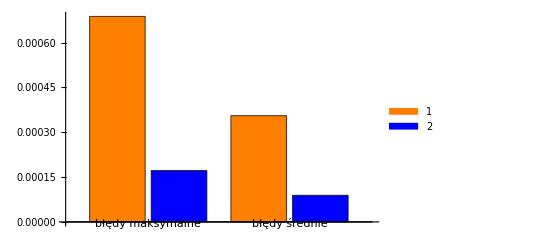

```mathematica
BarChart[{{N[Max[bbladbezwzgledny500]], N[Max[bbladbezwzgledny1000]]}, {N[Mean[bbladbezwzgledny500]], N[Mean[bbladbezwzgledny1000]]}}, ChartLabels -> {{"błędy maksymalne", "błędy średnie"},None},ChartStyle->{Orange,Blue}, ChartLegends->{"n=500", "n=1000"}]
```